## Homework 1

### Problem 2.3

#### Graph

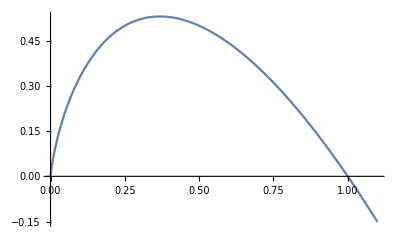

```mathematica
Plot[{-x Log[2,x]},{x,0,1.1}]
```

#### Functional Description

Define Simplification

```mathematica
FSc2p3[aa_]:=FullSimplify[aa,Assumptions->{pi∈Reals,pi≥0,p1∈Reals,p2∈Reals,p3∈Reals,p1≥0,p2≥0,p3≥0}]
```

Define Function

```mathematica
H[x_]:=-x Log[2,x]
```

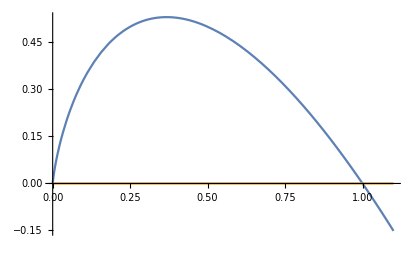

```mathematica
Plot[{H[x],H[x]+x Log[2,x]},{x,0,1.1}]
```

```mathematica
H[pi]//FSc2p3
```

-(pi Log[pi])/Log[2]

```mathematica
D[H[x],x]//FSc2p3
D[ D[H[x],x], x]//FSc2p3
D[H[pi],{pi,2}]//FSc2p3
```

-(1+Log[x])/Log[2]

-1/(x Log[2])

-1/(pi Log[2])

```mathematica
Solve[1==Log[2,x],x]
```

{{x→2}}

```mathematica
Log[2,ⅇ]//FSc2p3
```

1/Log[2]

```mathematica
FSc2p3[D[H[x],x]==-Log[2,ⅇ]-Log[2,x]]
```

True

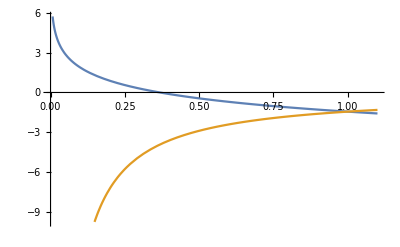

```mathematica
Plot[{FSc2p3[D[H[x0],x0]/.{x0->x}],FSc2p3[D[H[x0],{x0,2}]/.{x0->x}]},{x,0,1.1}]
```

```mathematica
D[H[x],x]/.{x->0}
D[H[x],x]/.{x->1}
```

∞

-1/Log[2]

```mathematica
Log[2,ⅇ]//FSc2p3
Log[2,ⅇ]//N
```

1/Log[2]

1.4427

```mathematica
D[H[x],{x,2}]/.{x->0}
D[H[x],{x,2}]/.{x->1}
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

-1/Log[2]

```mathematica
Solve[{0==D[H[x],x]},x]
Solve[{1==D[H[x],x]},x]
Solve[{-Log[2,ⅇ]==D[H[x],x]},x]
```

{{x→1/ⅇ}}

{{x→1/(2 ⅇ)}}

{{x→1}}

```mathematica
Solve[{0==D[H[x],x]},x]//N
Solve[{1==D[H[x],x]},x]//N
Solve[{-Log[2,ⅇ]==D[H[x],x]},x]//N
```

{{x→0.367879}}

{{x→0.18394}}

{{x→1.}}

```mathematica
NMaximize[FSc2p3[H[x]/.{x->pi}],pi]//FSc2p3
```

NMaximize::nrnum: The function value 0.224229  - 3.75756\ ⅈ is not a real number at {pi} = {-0.829053}.

General::stop: Further output of NMaximize :: nrnum will be suppressed during this calculation.

NMaximize[-(pi Log[pi])/Log[2],pi]

```mathematica
FindMaximum[FSc2p3[H[x]/.{x->pi}],pi]//FSc2p3
```

{0.530738,{pi→0.367879}}

```mathematica
H2[x_,y_]:=H[x]+H[y]
H3[x_,y_,z_]:=H[x]+H[y]+H[z]
```

```mathematica
Plot3D[H2[x,y],{x,0,1.1},{y,0,1.1}]
```

-Graphics3D-

```mathematica
FindMaximum[{H2[x,y]},{x,y}]
```

{1.06148,{x→0.367879,y→0.367879}}